```mathematica
f[n_]:=1132
```

```mathematica
∫_(-∞)^129.3 PDF[NormalDistribution[129.8,2.2],x]ⅆx
```

0.410106

```mathematica
∫_(-∞)^125 PDF[NormalDistribution[129.8,2.2,x]ⅆx
```

```mathematica
v[s_]:=(100800 √s)/(s+90)^2
```

```mathematica
vv[n_]:=v[10n]
```

```mathematica
Grid[Transpose[N[Table[{10n,v[10n],v[10n]-v[10(Max[n-1,0])]},{n,0,10}],4]],Frame->All]
```

0 | 10. | 20. | 30. | 40. | 50. | 60. | 70. | 80. | 90. | 100.
0 | 31.88 | 37.26 | 38.34 | 37.72 | 36.37 | 34.7 | 32.94 | 31.2 | 29.51 | 27.92
0 | 31.88 | 5.38 | 1.085 | -0.6178 | -1.357 | -1.664 | -1.758 | -1.747 | -1.682 | -1.592

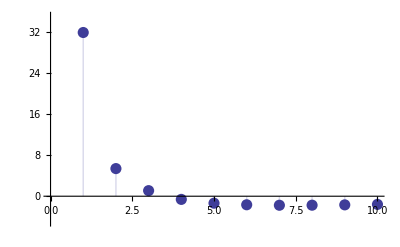

```mathematica
ListPlot[Table[v[10n]-v[10(Max[n-1,0])],{n,1,10}],Filling->Axis,PlotStyle->PointSize[0.02],PlotRange->{-5,35}]
```

```mathematica
N[1/100∫_0^100 v[s]ⅆs]
```

33.1953